```mathematica
(*Метод Эйлера*)
```

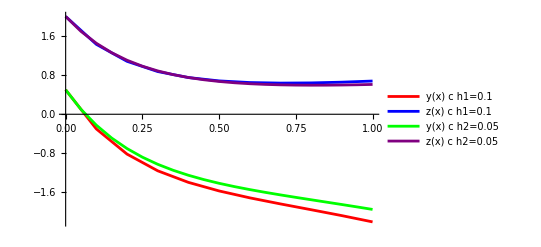

```mathematica
Clear[y, z]
a = 0;  b = 1;          y0 = 0.5;        z0 = 2;         h1 = 0.1;       h2 = 0.05;      
f[y_, z_] := 2-5*z;  
g[y_, z_, x_] := -3*z-y;
eulerMethod[{y0_, z0_}, h_, n_] := 
  Module[{x = a, y = y0, z = z0, result = {{x, y, z}}},
    AppendTo[result, {x, y, z}];  
    For[i = 1, i <= n, i++,
      y = y + h * f[y, z]; 
      z = z + h * g[y, z, x]; 
      x = x + h;
      AppendTo[result, {x, y, z}];  
    ];
    result
  ];

n1 = Floor[(b - a)/h1]; 
n2 = Floor[(b - a)/h2];
euler1 = eulerMethod[{y0, z0}, h1, n1];
euler2 = eulerMethod[{y0, z0}, h2, n2];

ListLinePlot[
 {
  euler1[[All, {1, 2}]], euler1[[All, {1, 3}]], 
  euler2[[All, {1, 2}]], euler2[[All, {1, 3}]]
 },
 PlotStyle -> {Red, Blue, Green, Purple},
 PlotLegends -> {"y(x) с h1=0.1", "z(x) с h1=0.1", 
   "y(x) с h2=0.05", "z(x) с h2=0.05"},

 PlotRange -> All
]
```

```mathematica
(*Метод Рунге-Кутта*)
```

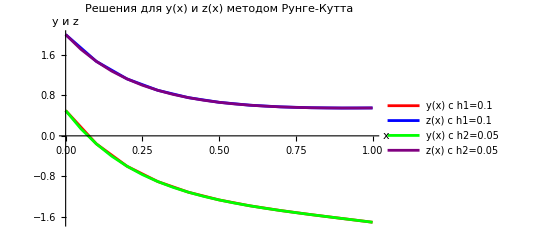

```mathematica
Clear[y,z]
a = 0;  b = 1;          y0 = 0.5;        z0 = 2;         h1 = 0.1;       h2 = 0.05;      
f[y_, z_] := 2-5*z;  
g[y_, z_, x_] := -3*z-y;

rungeKuttaMethod[{y0_,z0_},h_,n_]:=Module[{x=a,y=y0,z=z0,result={{x,y,z}}},AppendTo[result,{x,y,z}];
For[i=1,i<=n,i++,
{k1y,k1z}={h*f[y,z],h*g[y,z,x]};
{k2y,k2z}={h*f[y+0.5*k1y,z+0.5*k1z],h*g[y+0.5*k1y,z+0.5*k1z,x+0.5*h]};
{k3y,k3z}={h*f[y+0.5*k2y,z+0.5*k2z],h*g[y+0.5*k2y,z+0.5*k2z,x+0.5*h]};
{k4y,k4z}={h*f[y+k3y,z+k3z],h*g[y+k3y,z+k3z,x+h]};
y=y+(1/6) (k1y+2*k2y+2*k3y+k4y);
z=z+(1/6) (k1z+2*k2z+2*k3z+k4z);
x=x+h;
AppendTo[result,{x,y,z}];  ];
result];

n1=Floor[(b-a)/h1];
n2=Floor[(b-a)/h2];

rk1=rungeKuttaMethod[{y0,z0},h1,n1];
rk2=rungeKuttaMethod[{y0,z0},h2,n2];

ListLinePlot[{rk1[[All,{1,2}]],rk1[[All,{1,3}]],rk2[[All,{1,2}]],rk2[[All,{1,3}]]},PlotStyle->{Red,Blue,Green,Purple},PlotLegends->{"y(x) с h1=0.1","z(x) с h1=0.1","y(x) с h2=0.05","z(x) с h2=0.05"},AxesLabel->{"x","y и z"},PlotLabel->"Решения для y(x) и z(x) методом Рунге-Кутта",PlotRange->All]
```

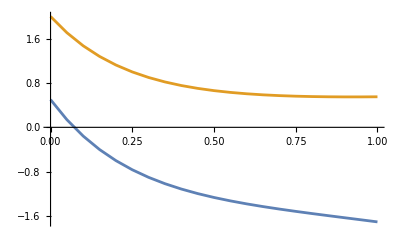

```mathematica
ListLinePlot[{rk2[[All,{1,2}]],rk2[[All,{1,3}]]},PlotRange->All]
```

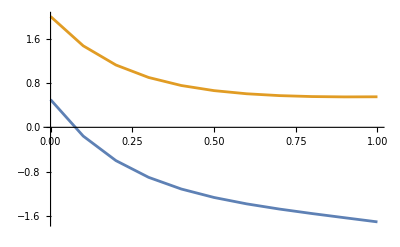

```mathematica
ListLinePlot[{rk1[[All,{1,2}]],rk1[[All,{1,3}]]},PlotRange->All]
```

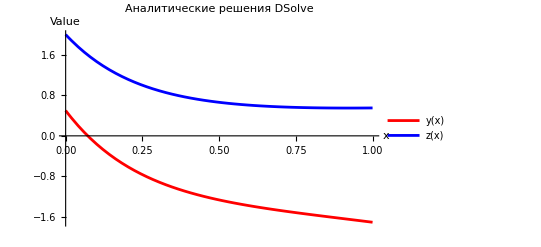

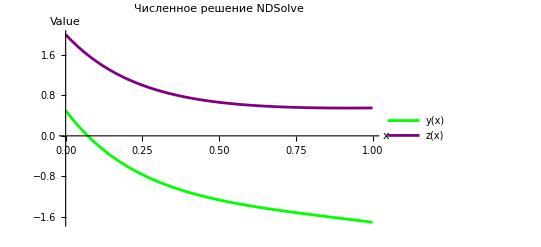

```mathematica
Clear[y,z]
eq1=y'[x]+5*z[x]==2; 
eq2=z'[x]+(y[x])+3*z[x]==0; 
initialConditions={y[0]==0.5,z[0]==2};

solutionDSolve=DSolve[{eq1,eq2,initialConditions},{y,z},x];
ySolution=y[x]/. solutionDSolve[[1]];
zSolution=z[x]/. solutionDSolve[[1]];

Plot[{ySolution,zSolution},{x,0,1},PlotStyle->{Red,Blue},PlotLegends->{"y(x)","z(x)"},AxesLabel->{"x","Value"},PlotLabel->"Аналитические решения DSolve"]

numericalSolution=NDSolve[{eq1,eq2,initialConditions},{y,z},{x,0,1}];

Plot[{y[x]/. numericalSolution,z[x]/. numericalSolution},{x,0,1},PlotStyle->{Green,Purple},PlotLegends->{"y(x)","z(x)"},AxesLabel->{"x","Value"},PlotLabel->"Численное решение NDSolve"]
```